```mathematica
SetDirectory["/home/rpb/worker-big/membrane-repository/pickle-repository/membrane-v614.md.part0002.skip10.protein2-framefilter/"];
Needs["PlotLegends`"]
```

```mathematica
framestotal=350;
```

```mathematica
lenscale=1.;
```

```mathematica
rot[th_]:={{Cos[th],-Sin[th]},{Sin[th],Cos[th]}}
```

#### Fixed axis

```mathematica
fx[x_,y_]:=-hpp*Exp[-(x-xcpp)^2/(2w1pp)]*Exp[-(y-ycpp)^2/(2w2pp)]
```

#### Fluid axis

```mathematica
fx[x_,y_]:=-hpp*Exp[-((x-xcpp)*Cos[theta]+(y-ycpp)*Sin[theta])^2/(2w1pp^2)]*Exp[-(-(x-xcpp)Sin[theta]+(y-ycpp)Cos[theta])^2/(2w2pp^2)]+zshift
```

```mathematica
curvfx[x_,y_]:=((1+D[fx[x,y],{x,1}]^2)D[fx[x,y],{y,2}]+(1+D[fx[x,y],{y,1}]^2)D[fx[x,y],{x,2}]-2*D[fx[x,y],{x,1}]*D[fx[x,y],{y,1}]*D[fx[x,y],{x,1},{y,1}])/(1+(D[fx[x,y],{x,1}])^2+(D[fx[x,y],{y,1}])^2)^(3/2)
```

#### Load parameters

```mathematica
filename="params.dat";
file=OpenRead[filename];
paramfile=ReadList[file,{Number,Number,Number,Number,Number,Number,Number}];
Close[file];
```

#### Framewise calculation of maximum curvature

```mathematica
Dynamic[frameno]
curves={};
domains={};
regions={};
maps={};
cplotzs={};
curves2={};
params={};
means={};
dats={};
Clear[a,b,c,ap,bp,cp,w1p,w2p,hp,xcp,ycp,w1,w2,h,xc,yc,zshift,t1];
For[frameno=1,frameno≤framestotal,frameno++,{Clear[a,b,c,ap,bp,cp,w1p,w2p,hp,xcp,ycp,w1,w2,h,xc,yc,zshift,t1];
If[frameno≠10000,{
If[MemberQ[FileNames[],filename],{
filename="framefilter."<>ToString[NumberForm[frameno,{4,0},NumberPadding->{"0",""}]]<>"dat";
file=OpenRead[filename];
rawfile=ReadList[file,{Number,Number,Number}];
Close[file];
datar=rawfile;
{a,b,c1,c2,w1,w2,t1}=paramfile[[frameno]];
curvfx2[x_,y_]=curvfx[x,y]/.{hpp->b,xcpp->c1,ycpp->c2,w1pp->Sqrt[Abs[w1]/2],w2pp->Sqrt[Abs[w1]/2],zshift->a,theta->t1};
AppendTo[curves2,Max[Table[curvfx2[lenscale*datar[[i,1]],lenscale*datar[[i,2]]],{i,1,Length[datar]}]]];
regplot=ListPlot[Table[{lenscale*datar[[i,1]],lenscale*datar[[i,2]]},{i,1,Length[datar]}],AspectRatio->1,PlotStyle->{{PointSize[0.006],Gray}}];
AppendTo[regions,regplot];
}];
}];
}];
```

ListPlot::lpn: {{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot::lpn: {{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

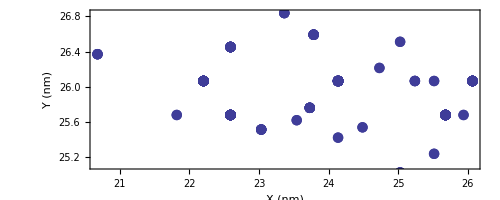

```mathematica
regions={};
For[frameno=1,frameno≤framestotal,frameno++,{Clear[a,b,c,ap,bp,cp,w1p,w2p,hp,xcp,ycp,w1,w2,h,xc,yc,zshift,t1];
If[frameno≠1000,{
If[MemberQ[FileNames[],filename],{
filename="framefilter."<>ToString[NumberForm[frameno,{4,0},NumberPadding->{"0",""}]]<>"dat";
file=OpenRead[filename];
rawfile=ReadList[file,{Number,Number,Number}];
Close[file];
datar=rawfile;
regplot=ListPlot[Table[{lenscale*datar[[i,1]]/10,lenscale*datar[[i,2]]/10},{i,1,Length[datar]}],AspectRatio->1,PlotStyle->{{PointSize[0.005],Gray}}];
AppendTo[regions,regplot];
}];
}];
}];
postraj=Table[{paramfile[[i,3]]/10,paramfile[[i,4]]/10},{i,1,Length[paramfile]}];
lptraj=ListPlot[postraj,Frame->True,ClippingStyle->Opacity[1],PlotStyle->{{PointSize[0.015]}},FrameLabel->{"X (nm)","Y (nm)","Gaussian Center locations",""},BaseStyle->{14,FontFamily->"Helvetica",Bold}];
plotregions=Show[Table[regions[[i]],{i,1,Length[regions],100}]];
Show[lptraj,plotregions,lptraj,AspectRatio->Automatic,ImageSize->500,Axes->False]
```

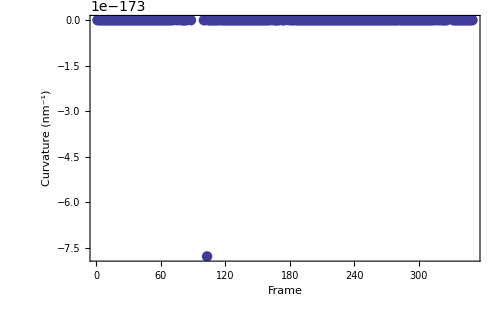

```mathematica
ListPlot[curves2*10,PlotRange->All,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Curvature (nm^-1)","Curvature",""},Axes->False,BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

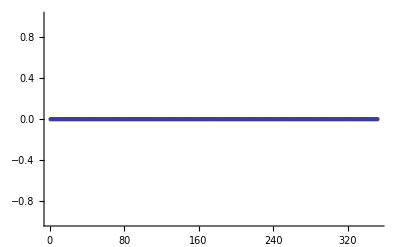

```mathematica
ListPlot[Sin[paramfile[[All,-1]]]]
```

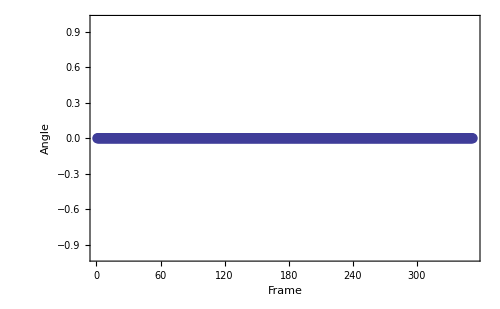

```mathematica
ListPlot[180Sin[paramfile[[All,-1]]],PlotRange->All,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Angle","Fitted gaussian angle",""},Axes->False,BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

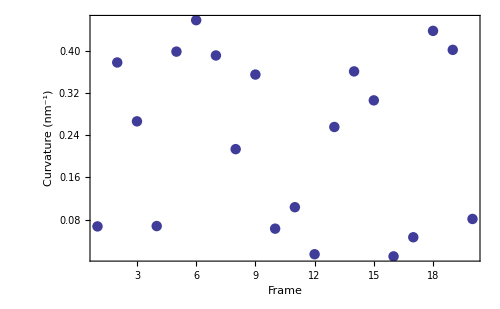

```mathematica
validinds=Position[Table[If[curves2[[i]]≤0.05&&curves2[[i]]≥0.001,1,0],{i,1,Length[curves2]}],1];
curvesv=Table[curves2[[validinds[[i,1]]]]*10.,{i,1,Length[validinds]}];
ListPlot[curvesv,PlotRange->All,ImageSize->500,Frame->True,PlotStyle->{{PointSize[0.015]}},FrameLabel->{"Frame","Curvature (nm^-1)","Filtered Curvature",""},Axes->False,BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

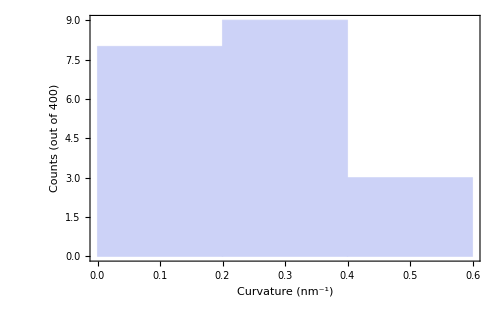

```mathematica
Histogram[curvesv,PlotRange->All,ImageSize->500,Frame->True,FrameLabel->{"Curvature (nm^-1)","Counts (out of 400)","Filtered maximum curvatures in the shadow",""},Axes->False,BaseStyle->{14,FontFamily->"Helvetica",Bold}]
```

```mathematica
{Sqrt[1/2*Mean[Table[Norm[paramfile[[validinds[[i]],5]]],{i,1,Length[validinds]}]]],Sqrt[1/2*Mean[Table[Norm[paramfile[[validinds[[i]],6]]],{i,1,Length[validinds]}]]]}
```

{11.9537,9.23019}

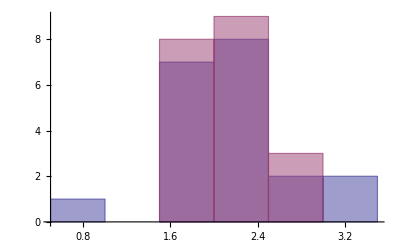

```mathematica
Histogram[{Table[Log[10,Norm[paramfile[[validinds[[i]],5]]]],{i,1,Length[validinds]}],Table[Log[10,Norm[paramfile[[validinds[[i]],6]]]],{i,1,Length[validinds]}]}]
```